# Laguerre polinomials

LaguerreL[n,x]gives the Laguerre polynomial L_n(x)which is the solution to EDO: x y^(..)+(1-x)ẏ+ny=0.
LaguerreL[n, k,x]gives the generalized Laguerre polynomial L_n^k(x)which is the solution to EDO: x y^(..)+(k+1-x)ẏ+ny=0.

#### Simple Laguerre L_n(x)

```mathematica
LaguerreL[0,x]
```

1

```mathematica
For[i=0,i<7,i++,Print[LaguerreL[i,x]]]
```

1

1-x

1/2 (2-4 x+x^2)

1/6 (6-18 x+9 x^2-x^3)

1/24 (24-96 x+72 x^2-16 x^3+x^4)

1/120 (120-600 x+600 x^2-200 x^3+25 x^4-x^5)

1/720 (720-4320 x+5400 x^2-2400 x^3+450 x^4-36 x^5+x^6)

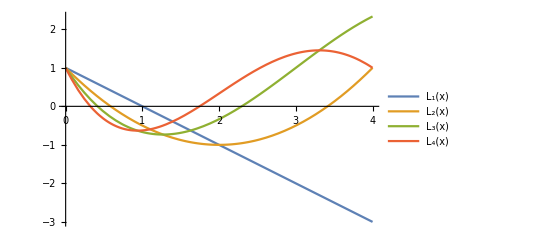

```mathematica
Plot[{LaguerreL[1,x],LaguerreL[2,x],LaguerreL[3,x],LaguerreL[4,x]},{x,0,4},PlotStyle->Thick,PlotLegends->"Expressions"]
```

#### Associated Laguerre L_n^k(x)

```mathematica
LaguerreL[n,μ,z]//TraditionalForm
```

L_n^μ(z)

```mathematica
LaguerreL[1,0,x]
```

1-x

```mathematica
For[i=0,i<6,i++,Print[LaguerreL[i,i,x]]]
```

1

2-x

1/2 (12-8 x+x^2)

1/6 (120-90 x+18 x^2-x^3)

1/24 (1680-1344 x+336 x^2-32 x^3+x^4)

1/120 (30240-25200 x+7200 x^2-900 x^3+50 x^4-x^5)

#### Print the Laguerre associatedL_n^k(x)

```mathematica
For[i=0,i<3,i++,For[j=0,j<3,j++,Print["(n,k)->","(",i,j,")","→",LaguerreL[i,j,x]]]]
```

(n,k)->(00)→1

(n,k)->(01)→1

(n,k)->(02)→1

(n,k)->(10)→1-x

(n,k)->(11)→2-x

(n,k)->(12)→3-x

(n,k)->(20)→1/2 (2-4 x+x^2)

(n,k)->(21)→1/2 (6-6 x+x^2)

(n,k)->(22)→1/2 (12-8 x+x^2)

#### Radial wave-function of the hydrogen atom:

We used the Bohr radio equal to 1.

```mathematica
ψ[n_,l_,r_]:=√(((n-l-1)!)/((n+l)!)) E^(-r/n) ((2r)/n)^l 2/n^2 LaguerreL[n-l-1, 2l+1,(2r)/n]
```

```mathematica
ψ[1,0,r]
```

2 ⅇ^-r

```mathematica
ψ[2,1,r]
```

(ⅇ^(-r/2) r)/(2 √6)

```mathematica
ψ[3,0,r]
```

(2 ⅇ^(-r/3) (27-18 r+2 r^2))/(81 √3)

#### Compute the energy eigenvalue from the differential equation:

```mathematica
energy[w_,r_, n_, l_]:=Simplify[1/w(D[w,r,r]+2/r D[w,r]-(l(l+1))/r^2 w+2/r w)]
```

The energy is independent of the orbital quantum number l:

```mathematica
Solve[(energy[ψ[n,l,r],r,n,l]-ℰ//FullSimplify)==0,ℰ]
```

{{ℰ→1/n^2}}